```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
(*Install["Vegas"]*)
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1;
```

### List of constants

```mathematica
EH=39.9;(*Hartree in meV*)
aB=3.17;(*Bohr radius in nm*)
Eshift=10;(*energy shift*)
numE=2;(*number of eigenenergies to be solved for*)
numL=10;
r0=5; (*scale radius*)
rc=0.2;
γ=0.208;(*effective mass ratio*)
maxcell=10^-4; (*maximum volume of the finite elements (relative to the volume of the total domain)*)
αmax=π/2.1;
pres=3;
```

```mathematica
(1/2)Integrate[Sin[θ]/(√(1-(1-x)(Cos[θ])^2)),{θ,0,π},Assumptions->x>0&&x<1]
```

-(ⅈ ArcCosh[√x])/(√(1-x))

```mathematica
y[x_]:=ArcTan[√((1-x)/x)]/(√(1-x));
```

```mathematica
κ=Limit[y[x],x-> γ]
```

1.23291

```mathematica
RkL[k_,L_,r_]:=Re[r Abs[Gamma[L+1-(I κ)/k]]/Factorial[2L+1] Exp[(π κ)/(2 k)](2k r )^L Exp[-I k r]Hypergeometric1F1[(I κ)/k+L+1,2L+2,2 I k r]];
```

```mathematica
PLm[L_,m_,θ_]:=√((2L+1)Factorial[L-m]/Factorial[L+m])LegendreP[L,m,Cos[θ]]
```

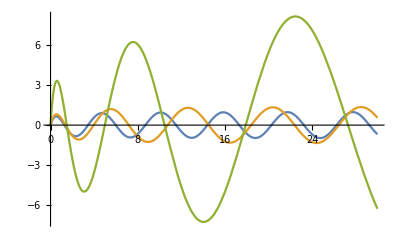

```mathematica
Plot[{RkL[1,0,r],RkL[√(2*0.25),0,r], RkL[√(2*0.001),0,r]},{r,0,30},PlotRange->All]
```

### Schrodinger equation and boundary conditions

```mathematica
U[r_]=Uc/(4π rc^3/3)HeavisideTheta[rc-r];
```

```mathematica
PDE0=-(1/2)D[f[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f[r,θ],θ]- 1/(2 r^2)D[f[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))+m^2/(2 r^2(Sin[θ])^2)-Wn) f[r,θ];
```

```mathematica
PDEc=-(1/2)D[f[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f[r,θ],θ]- 1/(2 r^2)D[f[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))-U[r]+m^2/(2 r^2(Sin[θ])^2)-Wn) f[r,θ];
```

```mathematica
PDE1=-(1/2)D[f1[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f1[r,θ],θ]- 1/(2 r^2)D[f1[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))- U[r]/3 KroneckerDelta[m,0]+m^2/(2 r^2(Sin[θ])^2)-Wn) f1[r,θ]-2 U[r]/3 KroneckerDelta[m,0]f2[r,θ];
PDE2=-(1/2)D[f2[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f2[r,θ],θ]- 1/(2 r^2)D[f2[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))-2 U[r]/3 KroneckerDelta[m,0]+m^2/(2 r^2(Sin[θ])^2)-Wn) f2[r,θ]-U[r]/3 KroneckerDelta[m,0]f1[r,θ];
```

```mathematica
PDEctn=Simplify[PDEc/. f-> (F[ArcTan[#1/r0],#2]&)/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ; (* transform to tangent space r = r0 tan[αr] to map [0, ∞] in r to [0, π/2] in αr*)
PDE0tn=Simplify[PDE0/. f-> (F[ArcTan[#1/r0],#2]&)/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;
PDE1tn=Simplify[PDE1/. {f1-> (F1[ArcTan[#1/r0],#2]&),f2-> (F2[ArcTan[#1/r0],#2]&)}/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ; 
PDE2tn=Simplify[PDE2/. {f1-> (F1[ArcTan[#1/r0],#2]&),f2-> (F2[ArcTan[#1/r0],#2]&)}/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;
```

```mathematica
Ω=ImplicitRegion[True,{{αr,0,αmax},{θ,0,Pi/2}}];
```

```mathematica
Γs=DirichletCondition[F[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γa=DirichletCondition[F[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; 
Γ1s=DirichletCondition[F1[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γ1a=DirichletCondition[F1[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; 
Γ2s=DirichletCondition[F2[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γ2a=DirichletCondition[F2[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; (*boundary condition for odd functions in θ'=π/2-θ*)
```

m=0 A1 even parity states

```mathematica
{E0e,f0e}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0,Uc-> 0},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0e=E0e-Eshift
```

{-0.783635,-0.22202}

m=0  odd parity states

```mathematica
{E0o,f0o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0,Uc-> 0},Γa},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0o=E0o-Eshift
```

{-0.288035,-0.137493}

m=1 odd parity states

```mathematica
{E1o,f1o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->1,Wn-> 0,Uc-> 0},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E1o=E1o-Eshift
```

{-0.160489,-0.0782101}

```mathematica
Ek=(4((E1o[[2]]+E0o[[2]])/2-E0e[[1]]))/3+E0e[[1]]
```

0.11741

### 4PI vs Ucc

```mathematica
UcL=Range[-0.2,0.8,0.005];
```

```mathematica
NPI4[Ucc_,Ek_]:=Module[{sols101,g101,sols112,g112,sols20,g201,g202,sols222,g222,sols301,g301,sols312,g312,sols332,g332,E0e,f0e,N0e,W,ω,x,k,l,L,p,M01,M02,M22,M42},
{E0e,f0e}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0,Uc-> Ucc},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
E0e=E0e-Eshift ;
N0e=ConstantArray[0,numE];
For[l=1,l<numE+1,l++,
N0e[[l]]=NIntegrate[(f0e[[l]])^2 r0 (Sec[αr])^2 Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];];
W[x_]=x+E0e[[1]];
ω=(Ek-E0e[[1]])/4;
sols101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g101[αr_,θ_]=sols101[[1,1,2]][αr,θ];
sols112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]]/2/.{m->1,Wn->  W[ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g112[αr_,θ_]=sols112[[1,1,2]][αr,θ];
sols20=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g101[αr,θ]/.{m->0,Wn->  W[2ω],Uc-> Ucc},PDE2tn==r0 Tan[αr]Sin[θ]g112[αr,θ]/.{m->0,Wn->  W[2ω],Uc-> Ucc}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g201[αr_,θ_]=sols20[[1,1,2]][αr,θ];
g202[αr_,θ_]=sols20[[1,2,2]][αr,θ];
sols222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g112[αr,θ]/2/.{m->2,Wn->  W[2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g222[αr_,θ_]=sols222[[1,1,2]][αr,θ];
sols301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g201[αr,θ]/.{m->0,Wn->  W[3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g301[αr_,θ_]=sols301[[1,1,2]][αr,θ];
sols312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g202[αr,θ]+g222[αr,θ])/2/.{m->1,Wn->  W[3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g312[αr_,θ_]=sols312[[1,1,2]][αr,θ];
sols332=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g222[αr,θ])/2/.{m->3,Wn->  W[3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g332[αr_,θ_]=sols332[[1,1,2]][αr,θ];
M01=ConstantArray[0,numL];
M02=ConstantArray[0,numL];
M22=ConstantArray[0,{2,numL}];
M42=ConstantArray[0,numL];
For[k=1,k<numL+1,k++,
Print[k];
M01[[k]]=1/(√N0e[[1]])NIntegrate[RkL[√(2 Ek),2(k-1),r0 Tan[αr]] PLm[2(k-1),0,θ]g301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 √γ Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,AccuracyGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
M02[[k]]=1/(√N0e[[1]])NIntegrate[RkL[√(2 Ek),2(k-1),r0 Tan[αr]] PLm[2(k-1),0,θ]g312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,AccuracyGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
M22[[1,k]]=1/(√N0e[[1]])NIntegrate[RkL[√(2 Ek),2k,r0 Tan[αr]] PLm[2k,2,θ](g312[αr,θ])r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,AccuracyGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
M22[[2,k]]=1/(√N0e[[1]])NIntegrate[RkL[√(2 Ek),2k,r0 Tan[αr]] PLm[2k,2,θ](g332[αr,θ])r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,AccuracyGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
M42[[k]]=1/(√N0e[[1]])NIntegrate[RkL[√(2 Ek),2(k+1),r0 Tan[αr]] PLm[2(k+1),4,θ]g332[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,AccuracyGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
];
Return[{E0e,N0e,M01,M02,M22,M42}];
]
```

```mathematica
datKL=NPI4[0,Ek]
```

1

2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3

4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

5

6

7

8

9

10

{{-0.783635,-0.22202},{3.03198,3.34554},{179.665,-28.7841,115.786,-513.268,-278.515,-78.6221,-16.1435,-2.69207,-0.396715,-0.055761},{-390.981,1097.11,760.5,207.067,40.7932,6.79171,1.0013,0.134546,0.0173921,0.00197603},{{-2564.17,-1395.28,-328.96,-59.4735,-9.33716,-1.3188,-0.17158,-0.0215765,-0.00260935,-0.000193027},{-198.789,-116.859,-25.2577,-3.55601,-0.432995,-0.0488714,-0.00536134,-0.00055707,-0.000218888,0.000159487}},{845.203,99.9021,10.7152,1.0997,0.110182,0.0109231,0.00101644,0.0000586051,-0.000135572,-0.000141023}}

m=0 A1 even parity states

```mathematica
{E0e,f0e}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0,Uc-> 0.417},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0e=E0e-Eshift
```

{-1.14108,-0.256892}

m=0  odd parity states

```mathematica
{E0o,f0o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0,Uc-> 0.417},Γa},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0o=E0o-Eshift
```

{-0.288233,-0.137563}

m=1 odd parity states

```mathematica
{E1o,f1o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->1,Wn-> 0,Uc-> 0.417},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E1o=E1o-Eshift
```

{-0.16054,-0.0782256}

```mathematica
Ek=(4((E1o[[2]]+E0o[[2]])/2-E0e[[1]]))/3+E0e[[1]]
```

0.236502

```mathematica
datSiP=NPI4[0.417,Ek]
```

1

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2

3

4

5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

7

8

9

10

{{-1.14108,-0.256892},{3.05078,3.23186},{-6.43173,18.7344,-10.7984,5.19141,7.08739,3.29553,1.05259,0.268905,0.0613808,0.0140535},{9.59298,-52.5883,-65.1162,-32.0055,-10.8941,-2.94341,-0.682533,-0.142075,-0.0277051,-0.00474598},{{106.894,115.075,50.1245,15.7348,4.01931,0.893746,0.180328,0.0341825,0.00603011,0.000742073},{11.2397,7.88216,1.53948,0.2547,0.0404789,0.00632664,0.000944595,0.0000983536,-7.28153×10^-6,-0.0001413}},{-52.3458,-5.78031,-0.742778,-0.100564,-0.0140125,-0.00196517,-0.000253522,-0.000162801,0.000120814,-0.000280943}}

```mathematica
DumpSave["4PI_SiP_v2.mx",{datKL,datSiP}]
```

{{{-0.783635,-0.22202},{3.03198,3.34554},{179.665,-28.7841,115.786,-513.268,-278.515,-78.6221,-16.1435,-2.69207,-0.396715,-0.055761},{-390.981,1097.11,760.5,207.067,40.7932,6.79171,1.0013,0.134546,0.0173921,0.00197603},{{-2564.17,-1395.28,-328.96,-59.4735,-9.33716,-1.3188,-0.17158,-0.0215765,-0.00260935,-0.000193027},{-198.789,-116.859,-25.2577,-3.55601,-0.432995,-0.0488714,-0.00536134,-0.00055707,-0.000218888,0.000159487}},{845.203,99.9021,10.7152,1.0997,0.110182,0.0109231,0.00101644,0.0000586051,-0.000135572,-0.000141023}},{{-1.14108,-0.256892},{3.05078,3.23186},{-6.43173,18.7344,-10.7984,5.19141,7.08739,3.29553,1.05259,0.268905,0.0613808,0.0140535},{9.59298,-52.5883,-65.1162,-32.0055,-10.8941,-2.94341,-0.682533,-0.142075,-0.0277051,-0.00474598},{{106.894,115.075,50.1245,15.7348,4.01931,0.893746,0.180328,0.0341825,0.00603011,0.000742073},{11.2397,7.88216,1.53948,0.2547,0.0404789,0.00632664,0.000944595,0.0000983536,-7.28153×10^-6,-0.0001413}},{-52.3458,-5.78031,-0.742778,-0.100564,-0.0140125,-0.00196517,-0.000253522,-0.000162801,0.000120814,-0.000280943}}}

```mathematica
K1=Total[(datSiP[[3]])^2]
```

598.176

```mathematica
datSiP[[5,1]]
```

{106.894,115.075,50.1245,15.7348,4.01931,0.893746,0.180328,0.0341825,0.00603011,0.000742073}

```mathematica
K2=Total[(datSiP[[4]])^2]+2Total[((datSiP[[5,1]]+datSiP[[5,2]])/2)^2]+2 Total[(datSiP[[6]]/2)^2]
```

25645.

```mathematica
K=K1/3+(2K2)/3
```

17296.

```mathematica
12^2
```

144

```mathematica
17000
```

```mathematica
150
```